```mathematica
Clear["Global`*"];(*Clear all variables*)
```

```mathematica
-Graphics-
(*考虑了2到5之间的电感，考虑中间的耦合电容Ck*)
```

```mathematica
Solve[{(f2-f5)/Ln-f5/Lg==f6/Lg-(f4-f6)/Ln},{f6}]
```

{{f6→(f2 Lg+f4 Lg-f5 Lg-f5 Ln)/(Lg+Ln)}}

```mathematica
f6 = (f2 Lg+f4 Lg-f5 Lg-f5 Ln)/(Lg+Ln);fd6 = (fd2 Lg+fd4 Lg-fd5 Lg-fd5 Ln)/(Lg+Ln);
T1 = 1/2*C12*(Φ0/(2*Pi))^2*(fd1-fd2)^2;
T2 = 1/2*C1g*(Φ0/(2*Pi))^2*(fd1)^2+1/2*C2g*(Φ0/(2*Pi))^2*(fd2)^2;
T3 = 1/2*C34*(Φ0/(2*Pi))^2*(fd3-fd4)^2;
T4 = 1/2*C3g*(Φ0/(2*Pi))^2*(fd3)^2+1/2*C4g*(Φ0/(2*Pi))^2*(fd4)^2;
T5 = 1/2*Ck*(Φ0/(2*Pi))^2*(fd5-fd6)^2;

T = T1+T2+T3+T4+T5;
U1 = 1/2*(Φ0/(2*Pi))^2*f5^2/Lg+1/2*(Φ0/(2*Pi))^2*(f5-f2)^2/Ln+(I0*Φ0)/(4*Pi)*f1^2;
U2 = 1/2*(Φ0/(2*Pi))^2*f6^2/Lg+1/2*(Φ0/(2*Pi))^2*(f6-f4)^2/Ln+(I0*Φ0)/(4*Pi)*f3^2;
U3 = 1/2*(Φ0/(2*Pi))^2*(f5-f6)^2/Lk;
U = U1+U2+U3;
```

```mathematica
L = T-U;
P1 = D[L,fd1];P2 = D[L,fd2];P3 = D[L,fd3];P4 = D[L,fd4];P5 = D[L,fd5];
R = {{Coefficient[P1,fd1,1],Coefficient[P1,fd2,1],Coefficient[P1,fd3,1],Coefficient[P1,fd4,1],Coefficient[P1,fd5,1]},
{Coefficient[P2,fd1,1],Coefficient[P2,fd2,1],Coefficient[P2,fd3,1],Coefficient[P2,fd4,1],Coefficient[P2,fd5,1]},
{Coefficient[P3,fd1,1],Coefficient[P3,fd2,1],Coefficient[P3,fd3,1],Coefficient[P3,fd4,1],Coefficient[P3,fd5,1]},
{Coefficient[P4,fd1,1],Coefficient[P4,fd2,1],Coefficient[P4,fd3,1],Coefficient[P4,fd4,1],Coefficient[P4,fd5,1]},
{Coefficient[P5,fd1,1],Coefficient[P5,fd2,1],Coefficient[P5,fd3,1],Coefficient[P5,fd4,1],Coefficient[P5,fd5,1]}
};
S = Inverse[R];
p  = {{p1},{p2},{p3},{p4},{p5}};
H =(1/2*Transpose[p].S.p+U)[[1,1]];
```

```mathematica
coeffp1 = Coefficient[H,p1,2];coefff1 = Coefficient[H,f1,2];
coeffp2 = Coefficient[H,p2,2];coefff2 = Coefficient[H,f2,2];
coeffp3 = Coefficient[H,p3,2];coefff3 = Coefficient[H,f3,2];
coeffp4 = Coefficient[H,p4,2];coefff4 = Coefficient[H,f4,2];
coeffp5 = Coefficient[H,p5,2];coefff5 = Coefficient[H,f5,2];
coeffp1p2 = Coefficient[H,p1*p2];coeffp1p5 = Coefficient[H,p1*p5];
coeffp2p5 = Coefficient[H,p2*p5];
coeffp3p4 = Coefficient[H,p3*p4];coeffp3p5 = Coefficient[H,p3*p5];
coeffp4p5 = Coefficient[H,p4*p5];
coefff2f4 = Coefficient[H,f2*f4];coefff2f5 = Coefficient[H,f2*f5];
coefff4f5 = Coefficient[H,f4*f5];

r1 = 2*coefff1;b1 = 2*coeffp1;
r2 = 2*coefff2;b2 = 2*coeffp2;
r3 = 2*coefff3;b3 = 2*coeffp3;
r4 = 2*coefff4;b4 = 2*coeffp4;
r5 = 2*coefff5;b5 = 2*coeffp5;

ω1 = Sqrt[r1*b1];ω2 = Sqrt[r2*b2];ω3 = Sqrt[r3*b3];ω4 = Sqrt[r4*b4];ω5 = Sqrt[r5*b5];
```

```mathematica
(***********************************************************************************************)
Nlevel =5;
adiag = N[Table[Sqrt[i],{i,Nlevel-1}]];idiag =  N[Table[1,{i,Nlevel}]];
a = N[DiagonalMatrix[adiag,1]];
i = N[DiagonalMatrix[idiag]];
a1 = KroneckerProduct[a,i,i,i,i];a1d = ConjugateTranspose[a1];
a2 = KroneckerProduct[i,a,i,i,i];a2d = ConjugateTranspose[a2];
a3 = KroneckerProduct[i,i,a,i,i];a3d = ConjugateTranspose[a3];
a4 = KroneckerProduct[i,i,i,a,i];a4d = ConjugateTranspose[a4];
a5 = KroneckerProduct[i,i,i,i,a];a5d = ConjugateTranspose[a5];
it = KroneckerProduct[i,i,i,i,i];
(***********************************************************************************************)
```

```mathematica
C12 = 66.0*10^-15;C1g =20.0*10^-15;C2g =100.0*10^-15;
C34 = 66.0*10^-15;C3g =20.0*10^-15;C4g =100.0*10^-15;
Ln = 0.300*10^-9;
Ck = 140.0*10^-15;
Lg = 0.450*10^-9;I0 = (280.0*10^-9*1000)/9000;Lc = 1.0*10^-9;
h = 6.62606896*10^-34;hbar = h/2.0/Pi;e = 1.60217662*10^-19;Φ0 = h/2/e;
Ikc = (280.0*10^-9*1000)/750;Lkc = Φ0/(2*Pi)*1/Ikc;
```

```mathematica
fn=Function[θ,
Block[{},

 Lk =Lkc/Cos[θ];
(*rule1 = {x_ y_ :>x.y,x_^2:>x.x};
rule2 = {(x_/;Element[x,Reals]).y_:>x*y};
H1 = Expand[H]//.rule1;
He = H1//.rule2;
He = coefff1*f1.f1+coefff2*f2.f2+coefff3*f3.f3+coefff6*f6.f6+coefff7*f7.f7+coefff8*f8.f8+coefff3f8*f3.f8+coeffp1*p1.p1+coeffp2*p2.p2+coeffp3*p3.p3+coeffp6*p6.p6+coeffp7*p7.p7+coeffp8*p8.p8+coeffp1p2*p1.p2+coeffp1p3*p1.p3+coeffp1p6*p1.p6+coeffp1p7*p1.p7+coeffp1p8*p1.p8+coeffp2p3*p2.p3+coeffp2p6*p2.p6+coeffp2p7*p2.p7+coeffp2p8*p2.p8+coeffp3p6*p3.p6+coeffp3p7*p3.p7+coeffp3p8*p3.p8+coeffp6p7*p6.p7+coeffp6p8*p6.p8+coeffp7p8*p7.p8;*)


f1 = Sqrt[hbar/2]*(b1/r1)^0.25*(a1+a1d);p1 =-I* Sqrt[hbar/2]*(r1/b1)^0.25*(a1-a1d);
f2 = Sqrt[hbar/2]*(b2/r2)^0.25*(a2+a2d);p2 =-I* Sqrt[hbar/2]*(r2/b2)^0.25*(a2-a2d);
f3 = Sqrt[hbar/2]*(b3/r3)^0.25*(a3+a3d);p3 =-I* Sqrt[hbar/2]*(r3/b3)^0.25*(a3-a3d);
f4 = Sqrt[hbar/2]*(b4/r4)^0.25*(a4+a4d);p4 =-I* Sqrt[hbar/2]*(r4/b4)^0.25*(a4-a4d);
f5 = Sqrt[hbar/2]*(b5/r5)^0.25*(a5+a5d);p5 =-I* Sqrt[hbar/2]*(r5/b5)^0.25*(a5-a5d);
He = hbar*ω1*(a1d.a1+it/2)+hbar*ω2*(a2d.a2+it/2)+hbar*ω3*(a3d.a3+it/2)+hbar*ω4*(a4d.a4+it/2)+hbar*ω5*(a5d.a5+it/2)+coeffp1p2*p1.p2+coeffp1p5*p1.p5+coeffp2p5*p2.p5+coeffp3p4*p3.p4+coeffp3p5*p3.p5+coeffp4p5*p4.p5+coefff2f4*f2.f4+coefff2f5*f2.f5+coefff4f5*f4.f5;



result = Sort[Eigenvalues[He]/h/10^6][[1;;5]];
freq = (result[[2]]-result[[1]])/10^3;

g = (result[[3]]-result[[1]]-(result[[2]]-result[[1]]))/2;
output = {freq,g}
]];
```

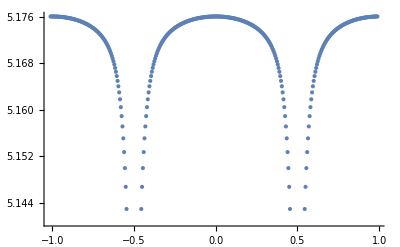

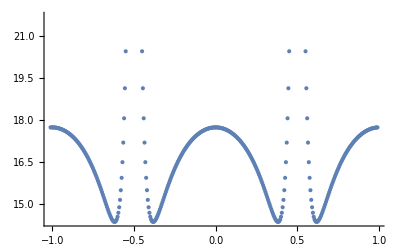

```mathematica
Φlist = N[Table[-1.01+n*2.0/400.0,{n,0,400}]];
f[Φ_]:=(ϕ/.(NSolve[hbar/(2*e)*ϕ+N[Lc]*Ikc*Sin[ϕ] == -Φ*Φ0,ϕ,Reals]))[[1]];
ϕlist = N[Parallelize[ Map[f,Φlist]]];
outputlist = Parallelize[ Map[fn,ϕlist]];
freqlist = outputlist[[;;,1]];
glist = outputlist[[;;,2]];

ListPlot[Table[{Φlist[[i]],freqlist[[i]]},{i,Length[Φlist]}]]
ListPlot[Table[{Φlist[[i]],glist[[i]]},{i,Length[Φlist]}]]
```

```mathematica
fn[0]
```

{5.17604,17.7375}